## Getting R_s, rho_s

```mathematica
hydroeq=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{tG,_Real},{t0,_Real}},Module[{n=Length@ρ,inv=ρ,ϕ=ρ,ψ=ρ,aϕ=ρ,bϕ=ρ,cϕ=ρ,dϕ=ρ,aψ=ρ,bψ=ρ,cψ=ρ,dψ=ρ,α=ρ,γ=ρ,δr=ρ,δρ=ρ,nρ=ρ,nσ=σ,nr=r},
Do[
Do[inv[[j]]=(nσ[[j]])^3/nρ[[j]],{j,1,n}];
Do[ϕ[[j]]=(nρ[[j]]^(5/3) inv[[j]]^(2/3)-nρ[[j-1]]^(5/3) inv[[j-1]]^(2/3))/(M[[j]]-M[[j-1]])+((t0/tG)^2 (M[[j]]+M[[j-1]]))/(2 π^2 (nr[[j]]+nr[[j-1]])^4),{j,2,n}];
Do[ψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])-1/2 π (nr[[j]]+nr[[j-1]])^2 (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
(**)
Do[aϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[bϕ[[j]]=-((5 (nρ[[j-1]]^(2/3) inv[[j-1]]^(2/3)))/(3 (M[[j]]-M[[j-1]]))),{j,2,n}];
Do[cϕ[[j]]=-((2 (t0/tG)^2 (M[[j]]+M[[j-1]]))/(π^2 (nr[[j]]+nr[[j-1]])^5)),{j,2,n}];
Do[dϕ[[j]]=(5 (nρ[[j]]^(2/3) inv[[j]]^(2/3)))/(3 (M[[j]]-M[[j-1]])),{j,2,n}];
Do[aψ[[j]]=(M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[bψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
Do[cψ[[j]]=-((M[[j]]-M[[j-1]])/(nr[[j]]-nr[[j-1]])^2)-π (nr[[j]]+nr[[j-1]]) (nρ[[j]]+nρ[[j-1]]),{j,2,n}];
Do[dψ[[j]]=1/2 (-π) (nr[[j]]+nr[[j-1]])^2,{j,2,n}];
(**)
α[[1]]=0;
Do[α[[j]]=(dϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-dψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
γ[[1]]=0;
Do[γ[[j]]=((bψ[[j]]-aψ[[j]] α[[j-1]]) (ϕ[[j]]-aϕ[[j]] γ[[j-1]])-(bϕ[[j]]-aϕ[[j]] α[[j-1]]) (ψ[[j]]-aψ[[j]] γ[[j-1]]))/(cϕ[[j]] (bψ[[j]]-aψ[[j]] α[[j-1]])-cψ[[j]] (bϕ[[j]]-aϕ[[j]] α[[j-1]])),{j,2,n}];
(**)
δρ[[n]]=0;
δr[[n]]=-γ[[n]];
Do[δρ[[n-j]]=-((ψ[[n-j+1]]-aψ[[n-j+1]] γ[[n-j]]+cψ[[n-j+1]] δr[[n-j+1]]+dψ[[n-j+1]] δρ[[n-j+1]])/(bψ[[n-j+1]]-aψ[[n-j+1]] α[[n-j]]));
δr[[n-j]]=-γ[[n-j]]-α[[n-j]]*δρ[[n-j]];,{j,1,n-1}];
(**)
If[Max[Table[Abs[δr[[j]]/r[[j]]],{j,1,n}]]<10^-4.(*corvergence criterion*),Break[]];
Do[nr[[j]]=nr[[j]]+δr[[j]],{j,1,n}];
Do[nρ[[j]]=nρ[[j]]+δρ[[j]],{j,1,n}];
Do[nσ[[j]]=(nρ[[j]]*inv[[j]])^(1/3),{j,1,n}];
,{k,0,10^10}];
(**)
{nr,nρ,nσ}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
heat=Compile[{{ρ,_Real,1},{r,_Real,1},{σ,_Real,1},{M,_Real,1},{ξ,_Real,1},{tG,_Real},{t0,_Real},{m,_Real},{r0,_Real},{ρ0,_Real}},
Module[{n=Length@ρ,nρ=ρ,nσ=σ,nr=r,nξ=ξ,κ=r,L=r,δucond=r,δusemi=r,δu=r,δT=r},
Do[κ[[j]]=((nσ[[j]]*(3/2 *(25(π)^(1/2))/32))^-1+(((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0))/tG)^2*(3/2*0.75*(16/π)^(1/2)* (nρ[[j]]*nσ[[j]]^3))^-1)^-1,{j,1,n}];
L[[1]]=0;
Do[L[[j]]=((2.18428*10^-6*m*t0)/(r0*nξ[[j]]*ρ0)(*tel*))/t0*4 π nr[[j]]^2*κ[[j]]*Piecewise[{{(nσ[[j+1]]^2-nσ[[j-1]]^2)/(nr[[j+1]]-nr[[j-1]]),1<j<n},{(-nσ[[j+2]]^2+4 nσ[[j+1]]^2-3 nσ[[j]]^2)/(nr[[j+2]]-nr[[j]]),j==1},{(3 nσ[[j]]^2-4 nσ[[j-1]]^2+nσ[[j-2]]^2)/(nr[[j]]-nr[[j-2]]),j==n}}],{j,2,n}];
Do[δucond[[j]]=Piecewise[{{(L[[j+1]]-L[[j-1]])/(M[[j+1]]-M[[j-1]]),1<j<n},{(-L[[j+2]]+4 L[[j+1]]-3 L[[j]])/(M[[j+2]]-M[[j]]),j==1},{(3 L[[j]]-4 L[[j-1]]+L[[j-2]])/(M[[j]]-M[[j-2]]),j==n}}],{j,1,n}];
Do[δu[[j]]=(δucond[[j]])/(3/2 nσ[[j]]^2),{j,1,n}];
δT[[1]]=(Max[Table[Abs[δu[[j]]],{j,1,n}]])^-1*10^-4.(*determination of the next time step*);
Do[nσ[[j]]=(Sqrt[2/3*((3/2 nσ[[j]]^2)+(δucond[[j]])*δT[[1]])]),{j,1,n}];
{δT,nσ}
]
,CompilationTarget->"C",RuntimeOptions->"Speed"];
(**)
(*concentration-mass relation*)
ρc=1.8791*(h^2)*1.4771*10^-7(*Solar Mass/(pc)^3, usually in Ayuki code: 1.8791*(h^2)*1.4771 *);
h=0.671; (*usually in Ayuki code: 0.671*)
a[z_]:=0.520+(0.905-0.520)*Exp[-0.617*z^1.21];
b[z_]:=-0.101+0.026*z;
c[M_,z_]:=10^a[z]*(M/((10^12)*(h^-1)(*Solar Mass*)))^b[z]*(13.3199/13.3199)(*5.26*(M/10^14)^-0.1*);
r0[M_,z_]:=(200*4/3 π*ρc)^(-1/3)*M^(1/3)*(c[M,z])^-1*10^-3(*in kpc*);
ρ0[M_,z_]:=M/(4 π*(r0[M,z]*10^3)^3) (1/(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]]))(*ρc/3*c[M,z]^3*(-(c[M,z]/(1+c[M,z]))+Log[1+c[M,z]])^-1*)(*in Solar Mass/pc^3*);
z=0;
Mi=10.0;(*match the range in "Evolution"*)
Mf=10.9;
NM=1;
δM=(Mf-Mi)/NM;
Do[M200[i]=10^(Mi+δM*i),{i,0,NM}];
Do[RS[i]=r0[M200[i],0],{i,0,NM}]
Do[DS[i]=ρ0[M200[i],0],{i,0,NM}]
Do[constC[i] = c[M200[i],0], {i,0,NM}]
Table[M200[i],{i,0,NM}]
Table[RS[i],{i,0,NM}]
Table[DS[i],{i,0,NM}]
Table[constC[i], {i,0,NM}]
Clear[Mi,Mf,NM,r0,ρ0,z,a,b,c,h,ρc,M];
```

{1.×10^10,7.94328×10^10}

{3.43182,8.44159}

{0.011371,0.00676539}

{13.3199,10.8044}

## NFW

```mathematica
(*kpcGev = 3.08567758*10^18*5.06*10^13;
Print["kpcGev:", kpcGev]
GyrGeV = 31556926*1.52*10^24;
Print["GyrGeV:", GyrGeV]
MGeV = 1.989*10^33*5.62*10^23/kpcGev^3;
Print["MGeV:", MGeV]*)
```

kpcGev:1.56135×10^32

GyrGeV:4.79665×10^31

MGeV:2.93676×10^-40

```mathematica
Subscript[f, NFW][x_]:=Log[1+x]-x/(1+x);
```

```mathematica
SetDirectory[NotebookDirectory[]];(*output directory*)
```

```mathematica
Do[(*mass loop*)
Print["M="<>ToString[Mi+δM*p]];
(*Set up initial r-grid in Log-bin*)
ri=-2.(*Log10[Subscript[r, i=1]/Subscript[r, 0]]*);(*-4 for rSIDM*)
rf=2.(*Log10[Subscript[r, i=NR]/Subscript[r, 0]]*);(*2 for rSIDM*)
NR=2000;(*400 for Ayuki code,700 for rSIDM*)
δR=(rf-ri)/NR;
(*NFW scale parameters for given halo mass*)
rs=RS[p](*in kpc*);
ρs=DS[p](*in Solarmass/pc^3*);
(**)
G=1/(1.220890 10^19)^2(*GeV^-2*);
m=1(*GeV*)(*dummy variable: do not change this!*);
r0=rs*1.56 10^35(*in GeV^-1,1 kpc*);
t0=4.80 10^40(*in GeV^-1*)(*1 Gyr*);
ρ0=(ρs)*2.94*10^-40(*Gev^4,Solarmass/pc^3*);
tG=√(1/(4 π G ρ0));
(*RADI*)
r[0]=0;
Do[r[j]=10^(ri+δR*(j-1)),{j,1,NR+1}];
(*DENSITY*)
rho[0] = NIntegrate[(4π*x^2)/(x*(1+x)^2),{x,0,10^ri}]*((4/3)π*10^(3*ri))^-1;(*assumed NFW*);
Do[rho[j] = 1/(r[j]/1(1+r[j]/1)^2),{j, 1, NR+1}];
(*MASS*)
M[0] = 0;
Do[M[j] = 4π 1 1^3*Subscript[f, NFW][r[j]/1], {j,1,NR+1}];
(*nu*)
nu[0]= Limit[Sqrt[(t0/tG)^2*(1/(2 r (1+r)^2 1 1)(r (-1+r (-9-7 r+π^2 (1+r)^2))+r^4 Log[1+1/r]+Log[1+r]+r (-r (1+2 r) Log[r]+Log[1+r] (-2-4 r (2+r)+3 r (1+r)^2 Log[1+r]))+6 r^2 (1+r)^2 PolyLog[2,-r]) (1+r/1)^2)],{r->0}];
Print["nu[0]", nu[0]];
Do[nu[j] = Sqrt[(t0/tG)^2*(1/(2 r (1+r)^2 1 1)(r (-1+r (-9-7 r+π^2 (1+r)^2))+r^4 Log[1+1/r]+Log[1+r]+r (-r (1+2 r) Log[r]+Log[1+r] (-2-4 r (2+r)+3 r (1+r)^2 Log[1+r]))+6 r^2 (1+r)^2 PolyLog[2,-r]) (1+r/1)^2)]/.{r->r[j]}, {j,1,NR+1}];
(*OUTPUT*)
Print["Exporting data..."];
dataρsolfinal=Table[{r[j],rho[j], M[j], nu[j]},{j,0,NR+1}];
Export["PureNFW_M_"<>ToString[10.0]<>".txt",dataρsolfinal,"Table"];

,{p,0,0}];(*change it to {p,0,NM} to scan halo masses*)
Print["Job ended."]
```

M=0. + Mi

nu[0]0.

Exporting data...

Job ended.

```mathematica
kpcSI=3.08567758*10^(19) (*[m]*)
MsolarSI=1.98847*10^(30) (*[kg]*)
rhos = 17200000.0 (*[M_solar/kpc^3]*)
rs = 6.32 (*[kpc]*)
constG = 6.67*10^(-11) * (1/MsolarSI)^(-1)*(1/kpcSI)^(2)
rhosSI = 17200000.0  * MsolarSI * kpcSI^(-3)(*[kg/m^3]*)
rsSI = 6.32 *kpcSI(*[m]*)
constGSI = 6.67*10^(-11)(*[m/s^2 * kg-1 * m^2]*)
Subscript[ρ, NFW][r_]:= Subscript[ρ, s]/(r/Subscript[R, s](1+r/Subscript[R, s])^2)
Subscript[f, NFW][x_]:=Log[1+x]-x/(1+x)
Subscript[M, NFW][r_]:=4π Subscript[ρ, s] Subscript[R, s]^3*Subscript[f, NFW][r/Subscript[R, s]]
```

3.08568×10^19

1.98847×10^30

1.72×10^7

6.32

1.39298×10^-19

1.16411×10^-21

1.95015×10^20

```mathematica
6.67*^-11
```

```mathematica
(*DATA*)
ri=-2.(*Log10[Subscript[r, i=1]/Subscript[r, 0]]*);(*-4 for rSIDM*)
rf=2.(*Log10[Subscript[r, i=NR]/Subscript[r, 0]]*);(*2 for rSIDM*)
NR=2000;(*400 for Ayuki code,700 for rSIDM*)
δR=(rf-ri)/NR;
```

```mathematica
DSolve[ν2'[r]== -G (Subscript[M, NFW][r])/r^2-(Subscript[ρ, NFW]'[r])/(Subscript[ρ, NFW][r])ν2[r] ,ν2[r],r]
```

{{ν2[r]→r C[1] (r+R_s)^2-1/R_s 2 G π r (r+R_s)^2 (Log[r]-Log[r+R_s]-6 Log[1+r/R_s] Log[r+R_s]+3 Log[r+R_s]^2-6 PolyLog[2,-r/R_s]+(R_s (r (7+6 Log[1+r/R_s])+2 R_s))/(r (r+R_s))+1/(r^2 (r+R_s)^2)R_s^2 (r^2-r (r+R_s)+4 r Log[1+r/R_s] (r+R_s)-Log[1+r/R_s] (r+R_s)^2)) ρ_s}}

```mathematica
LogLogPlot[((r) C[1] (r+Subscript[R, s])^2-4 G π (r) Subscript[R, s]^3 (r+Subscript[R, s])^2 ((3 Log[r])/Subscript[R, s]^4-(3 Log[1+r/Subscript[R, s]]^2)/(2 Subscript[R, s]^4)-(3 Log[r+Subscript[R, s]])/Subscript[R, s]^4-(3 PolyLog[2,-r/Subscript[R, s]])/Subscript[R, s]^4+1/(r Subscript[R, s]^3)-(2 (-Log[1+r/Subscript[R, s]]/r+Log[r]/Subscript[R, s]-Log[r+Subscript[R, s]]/Subscript[R, s]))/Subscript[R, s]^3+1/(2 Subscript[R, s]^2 (r+Subscript[R, s])^2)+2/(Subscript[R, s]^3 (r+Subscript[R, s]))+(1+Log[1+r/Subscript[R, s]])/(Subscript[R, s]^3 (r+Subscript[R, s]))-((r)^2 (Log[r]-Log[r+Subscript[R, s]])+r Subscript[R, s]+Log[1+r/Subscript[R, s]] Subscript[R, s]^2)/(2 (r)^2 Subscript[R, s]^4)) Subscript[ρ, s])^(1/2)/.{Subscript[ρ, s]->rhos, Subscript[R, s]->rs, G->constG, C[1] ->0},{r,0, 100}, AxesLabel->{kpc, m/s}]
```

-Graphics-

```mathematica
1/(Subscript[ρ, NFW][r])Integrate[(Subscript[f, NFW][x])/(x^3(1+x)^2),{x,r,∞}]
```

ConditionalExpression[1/(2 r (1+r)^2 R_s ρ_s)(r (-1+r (-9-7 r+π^2 (1+r)^2))+r^4 Log[1+1/r]+Log[1+r]+r (-r (1+2 r) Log[r]+Log[1+r] (-2-4 r (2+r)+3 r (1+r)^2 Log[1+r]))+6 r^2 (1+r)^2 PolyLog[2,-r]) (1+r/R_s)^2, Re[r]>0&&Im[r]==0]

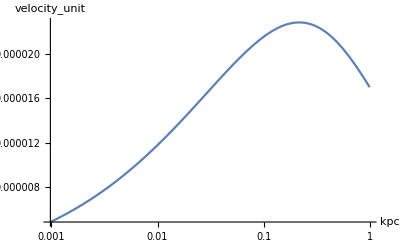

```mathematica
LogLinearPlot[√(1/(2 r (1+r)^2 Subscript[R, s] Subscript[ρ, s])(r (-1+r (-9-7 r+π^2 (1+r)^2))+r^4 Log[1+1/r]+Log[1+r]+r (-r (1+2 r) Log[r]+Log[1+r] (-2-4 r (2+r)+3 r (1+r)^2 Log[1+r]))+6 r^2 (1+r)^2 PolyLog[2,-r]) (1+r/Subscript[R, s])^2)/.{Subscript[ρ, s]->rhos, Subscript[R, s]->rs, G->constG},{r,0, 1}, AxesLabel->{kpc, velocity_unit}]
```

```mathematica
Limit[√(1/(2 r (1+r)^2 Subscript[R, s] Subscript[ρ, s])(r (-1+r (-9-7 r+π^2 (1+r)^2))+r^4 Log[1+1/r]+Log[1+r]+r (-r (1+2 r) Log[r]+Log[1+r] (-2-4 r (2+r)+3 r (1+r)^2 Log[1+r]))+6 r^2 (1+r)^2 PolyLog[2,-r]) (1+r/Subscript[R, s])^2)/.{Subscript[ρ, s]->rhos, Subscript[R, s]->rs, G->constG},r->0]
```

0.